```mathematica
Get["Rubi`"]
assumptions={x>0,ω∈Reals,ℰ∈Reals,σ>0};
𝒮[x_]:=Simplify[x,assumptions];
ℱ𝒮[x_]:=FullSimplify[x,assumptions];

𝒩[σ_]:=NormalDistribution[0,σ];
𝒰[x_]:=UniformDistribution[{-x,x}];
```

```mathematica
𝒮[Integrate[Cos[(ℰ-ω)t/2]^2*PDF[𝒩[σ],t],{t,-∞,∞}]]
```

1/2 (1+ⅇ^(-1/2 σ^2 (ℰ-ω)^2))

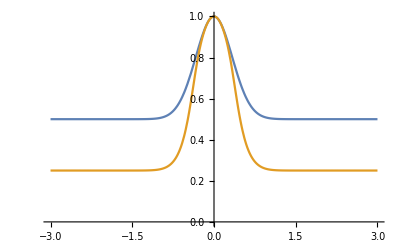

```mathematica
Plot[{1/2 (1+ⅇ^(-1/2 3^2 x^2)),Piecewise[{{1,x==0}},Exp[NIntegrate[Log[Cos[x*t/2]^2]PDF[𝒩[3],t],{t,-∞,∞},MaxRecursion->20,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->10}}]]]},{x,-3,3},PlotRange->{0,1}]
```

```mathematica
Simplify[D[Log[√((4^-n (1-p))/(4^-n (1-p)+p))],n],{p≥0,p≤1}]
```

-(2^(-1+2 n) p Log[4])/(1+(-1+4^n) p)

```mathematica
Limit[Simplify[D[Log[√((4^-n (1-p))/(4^-n (1-p)+p))],n],{p≥0,p≤1}],n->Infinity]
```

-Log[4]^2/Log[16]

```mathematica
TimeArray[σ_,prod_]:=Table[RandomVariate[𝒩[σ]],{k,1,prod}];
SingleRunProbAllZero[x_,timearray_]:=Product[Cos[x*timearray[[k]]]^2,{k,1,Length[timearray]}];
SingleRunMeasure[e_,ℰ_,timearray_,shots_]:=RandomVariate[BinomialDistribution[shots,Sum[SingleRunProbAllZero[e[[k]]-ℰ,timearray],{k,1,Length[e]}]/Length[e]]]/shots;

SingleRunPlot[n_,σ_,min_,max_,color_]:=With[{timearray=TimeArray[σ,n]},Plot[SingleRunProbAllZero[ℰ,timearray],{ℰ,min,max},PlotRange->{0,1},AxesLabel->{"E_j-ℰ",Subscript[P̄, n]},PlotStyle->{Thin,color},TicksStyle->Directive[FontOpacity->1,FontSize->8]]];
RodeoRoundPlot[n_,σ_,e_,shots_,evalreps_,min_,max_,diff_,join_,color_]:=DiscretePlot[Sum[With[{timearray=TimeArray[σ,n]},SingleRunMeasure[e,ℰ,timearray,shots]],{k,1,evalreps}]/evalreps,{ℰ,min,max,diff},Joined->join,PlotRange->{0,1},AxesLabel->{"E_j-ℰ",Subscript[P̄, n]},PlotStyle->{Thin,color},TicksStyle->Directive[FontOpacity->1,FontSize->8]];
```

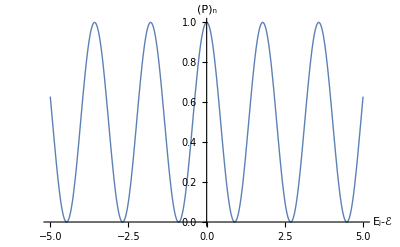
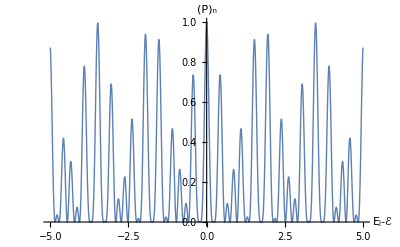
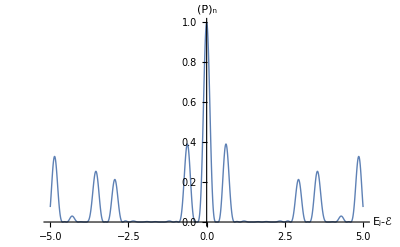

```mathematica
Table[SingleRunPlot[n,10,5,Default],{n,{1,2,4}}]
```

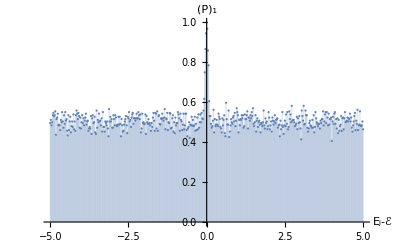
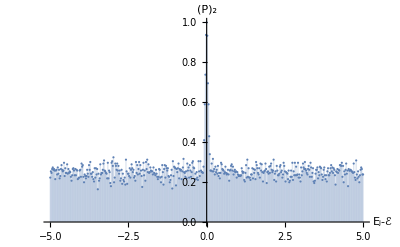
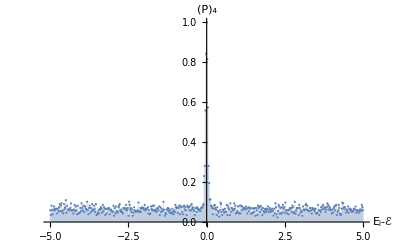

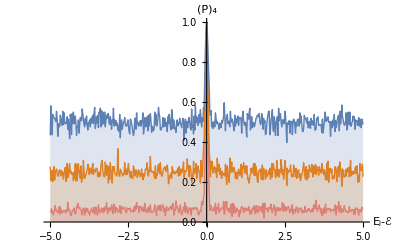

```mathematica
Table[RodeoRoundPlot[n,10,{0},1,256,-2,2,1/25,False,Default],{n,{1,2,4}}]
Show[RodeoRoundPlot[4,10,{0},1,256,-2,2,1/25,True,Pink],RodeoRoundPlot[2,10,1,256,5,1/50,True,Orange],RodeoRoundPlot[1,10,{0},1,256,-2,2,1/25,True,Default],PlotRange->All]
```

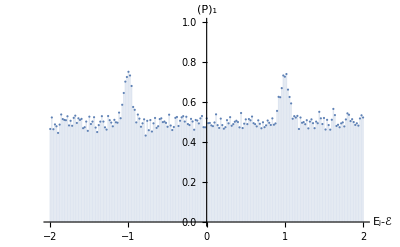

```mathematica
RodeoRoundPlot[1,10,{1,-1},1024,100,-2,2,1/50,False,Default]
```

```mathematica
N[With[{n=1,e={1,-1},evals=1},(Sum[With[{timearray=TimeArray[10,n]},Sum[SingleRunProbAllZero[e[[k]]-0,timearray],{k,1,Length[e]}]/Length[e]],{k,1,evals}]/evals)^(-1/n)]]
```

```mathematica
DiscretePlot[Sum[With[{e={1,-1}},(Sum[With[{timearray=TimeArray[10,n]},Sum[SingleRunProbAllZero[e[[k]]-0,timearray],{k,1,Length[e]}]/Length[e]],{k,1,n}]/n)^(-1/n)],{j,1}]/1,{n,1,1000},PlotRange->{{0,1000},{2,4}}]
```

$Aborted

```mathematica
𝒮[Integrate[Cos[θ]^2*PDF[𝒩[σ],θ],{θ,-∞,∞}]]
𝒮[Integrate[Cos[θ]^2*PDF[𝒰[π],θ],{θ,-π,π}]]
```

ⅇ^(-σ^2) Cosh[σ^2]

1/2

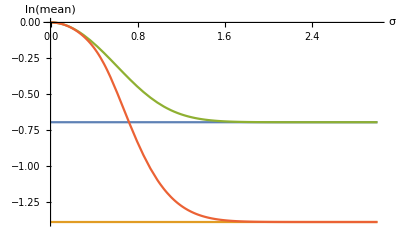

```mathematica
Plot[{-Log[2],-Log[4],Log[ⅇ^(-σ^2) Cosh[σ^2]],Piecewise[{{0,σ==0}},NIntegrate[Log[Cos[θ]^2]PDF[𝒩[σ],θ],{θ,-∞,∞},MaxRecursion->20,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->10}}]]},{σ,0,3},PlotRange->All,AxesLabel->{σ,ln[mean]}]
```

```mathematica
𝒮[Exp[Int[Log[Cos[θ]^2]PDF[𝒩[σ],θ],{θ,-∞,∞}]]]
𝒮[Exp[Integrate[Log[Cos[θ]^2]PDF[𝒰[π],θ],{θ,-π,π}]]]
```

ⅇ^(-Limit[1/2 Erf[θ/(√2 σ)] Log[Cos[θ]^2]+√2 Subst[Int[Erf[θ/σ] Tan[√2 θ],θ],θ,θ/(√2)],θ→-∞]+Limit[1/2 Erf[θ/(√2 σ)] Log[Cos[θ]^2]+√2 Subst[Int[Erf[θ/σ] Tan[√2 θ],θ],θ,θ/(√2)],θ→∞])

1/4

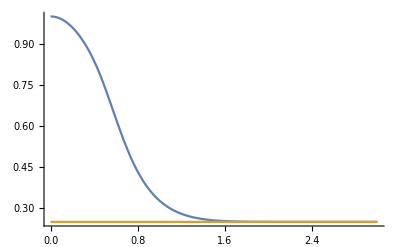

```mathematica
Plot[{Piecewise[{{1,σ==0}},Exp[NIntegrate[Log[Cos[θ]^2]PDF[𝒩[σ],θ],{θ,-∞,∞},MaxRecursion->20,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->10}}]]],1/4},{σ,0,3},PlotRange->All]
```

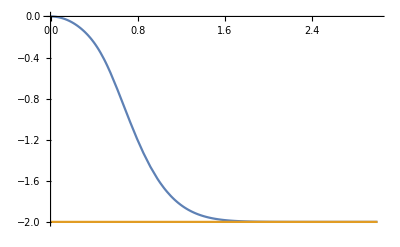

```mathematica
Plot[{Piecewise[{{0,σ==0}},NIntegrate[Log[Cos[θ]^2]PDF[𝒩[σ],θ],{θ,-∞,∞},MaxRecursion->20,Method->{"SymbolicDomainDecomposition",Method->{"LocalAdaptive",MinRecursion->10}}]/Log[2]],Log[2,1/4]},{σ,0,3},PlotRange->All]
```

```mathematica
P0[θ_]:=Cos[θ]^2;
ProductCos[n_,θ_]:=Product[P0[Subscript[θ, k]],{k,1,n}]
ProductCosSample[n_,m_]:=With[{r=RandomVariate[𝒰[π],{n,m}]},Table[Product[P0[r[[k]][[j]]],{k,1,n}],{j,1,m}]];
ProductCosDistribution[n_]:=ProbabilityDistribution[ProductCos[n,θ],Sequence@@Table[{Subscript[θ, k],-π,π},{k,1,n}]]
ProductCosExpectation[n_]:=Expectation[ProductCos[n,θ],Table[Subscript[θ, k]\[Distributed]𝒰[π],{k,1,n}]]
ProductCosLogPlot[n_,m_]:=Show[DiscretePlot[Log[Mean[ProductCosSample[k,m]]],{k,0,n},PlotStyle->Darker[Green],Filling->None,Joined->True],Plot[{-Log[2]x,-Log[4]x},{x,0,n},PlotStyle->{Thin,Thin}]]
ProductCosLogListPlot[s_,list_]:=Show[DiscretePlot[list[[k+1]],{k,0,Length[list]-1},PlotRange->{-Log[4]Length[list],0},PlotStyle->Darker[Green],Filling->None,Joined->True,PlotLabel->"s="<>ToString[s],AxesLabel->{n,"ln[Π_ncos^2(θ_k)]"}],Plot[{-Log[2]x,-Log[4]x},{x,0,Length[list]},PlotStyle->{}]]
```

```mathematica
𝒴[y_]:=Sqrt[1/(Exp[-y]-1)]/π;
𝕐[y_]:=1-(2/π)ArcTan[Sqrt[ⅇ^-y-1]];
```

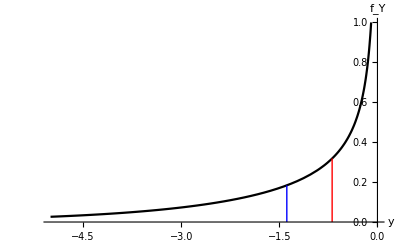

```mathematica
Show[Plot[Sqrt[1/(Exp[-y]-1)]/π,{y,-5,0},PlotRange->{0,1},AxesLabel->{y,Subscript[f, Y]},PlotStyle->{Black},TicksStyle->Directive[FontOpacity->1,FontSize->8]],Graphics[{Blue,Line[{{-Log[4],0},{-Log[4],𝒴[-Log[4]]}}],Red,Line[{{-Log[2],0},{-Log[2],𝒴[-Log[2]]}}]}]]
```

```mathematica
𝒮[Integrate[z*𝒴[z],{z,-Infinity,0}]]
```

-Log[4]

```mathematica
𝒮[Integrate[𝒴[z],{z,-Infinity,y}]]
```

```mathematica
Solve[𝕐[y]==1/2,y]
```

{{y→-Log[2]}}

```mathematica
𝒮[Integrate[(z-(-Log[4]))^2*𝒴[z],{z,-Infinity,0}]]
```

π^2/3

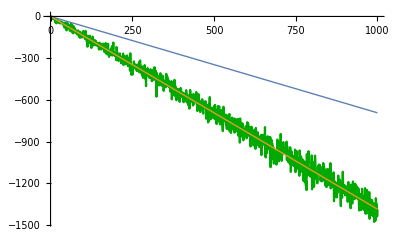

```mathematica
ProductCosLogPlot[1000,1]
```

```mathematica
"LOG OF MEAN";
GraphicsGrid[{
{ProductCosLogListPlot[1,{0,-0.16076,-0.0810663,-3.73946,-1.69353,-5.97891,-3.81222,-7.04391,-6.59305,-19.9544,-2.76671,-20.4759,-10.9947,-17.4892,-27.2588,-21.8489,-16.965,-42.4726,-20.2081,-28.1089,-24.3697,-30.4496,-38.2325,-28.8361,-27.9845,-59.4739,-32.9135,-43.8767,-33.9457,-44.7213,-53.8543,-37.2357,-37.6853,-39.3293,-53.5615,-49.9779,-61.5628,-63.6151,-42.4375,-41.3818,-59.8355,-41.3553,-57.1194,-67.5261,-47.5636,-56.8532,-50.7597,-64.2306,-76.2761,-59.0075,-68.7726,-55.7617,-56.4666,-66.2477,-72.3965,-52.6594,-71.9839,-80.2575,-79.0123,-106.609,-99.7077,-77.7601,-82.7597,-71.7153,-94.9433,-134.436,-85.9844,-86.4288,-82.8599,-82.6037,-130.316,-105.964,-103.107,-96.9627,-105.216,-112.95,-103.676,-91.35,-89.6396,-97.4642,-103.905,-118.063,-114.639,-126.509,-98.4208,-127.845,-125.509,-122.27,-91.702,-128.8,-158.136,-114.647,-143.918,-149.62,-160.155,-131.292,-150.383,-125.988,-159.874,-103.697,-136.103}],
ProductCosLogListPlot[10,{0,-0.867521,-1.01901,-1.94977,-3.29695,-2.47065,-2.82964,-5.69027,-7.91435,-7.32471,-6.83716,-9.5104,-8.11721,-10.0855,-14.1287,-16.8659,-10.1975,-15.8034,-18.6946,-16.4593,-18.0286,-19.6973,-19.1297,-18.4926,-27.2454,-20.8901,-31.6423,-24.3351,-29.203,-25.009,-36.1879,-27.9882,-31.839,-27.4753,-40.3537,-37.3314,-45.5918,-37.6423,-36.5794,-36.7394,-45.6898,-42.3639,-48.0194,-48.938,-42.3888,-58.6869,-63.156,-48.4734,-46.741,-59.219,-53.4443,-63.206,-40.191,-52.1374,-57.81,-64.7524,-66.2546,-57.7671,-61.5934,-65.4514,-64.0035,-68.37,-64.3101,-70.0741,-57.3587,-66.1801,-57.8426,-81.8819,-83.6481,-74.7377,-72.4975,-83.3917,-72.7956,-67.109,-86.1815,-87.2242,-83.0053,-88.6855,-78.6896,-98.1043,-85.5277,-101.313,-85.0776,-100.779,-88.7781,-99.285,-69.9572,-97.141,-109.713,-100.303,-93.4202,-100.497,-95.9596,-104.226,-114.482,-100.321,-95.1311,-95.6363,-108.295,-114.304,-117.824}],
ProductCosLogListPlot[100,{0,-0.684514,-1.5001,-1.91738,-2.81931,-3.62665,-3.76616,-4.4589,-5.43881,-6.23934,-7.96489,-9.18696,-8.37365,-9.86258,-6.66037,-10.3494,-12.1166,-11.5486,-10.8833,-16.5859,-18.134,-15.1169,-18.2486,-18.0049,-18.1659,-20.347,-22.2245,-22.9724,-22.3603,-17.7383,-21.1618,-25.7886,-25.9098,-25.5727,-24.0255,-32.3009,-29.8687,-31.7218,-36.6061,-29.5377,-27.064,-37.5994,-38.6031,-42.8186,-34.1934,-43.3019,-37.634,-47.107,-44.8725,-33.6409,-52.8066,-46.4919,-46.9854,-45.6687,-58.5746,-56.634,-57.2096,-52.9368,-51.8993,-58.768,-59.2604,-60.0641,-63.8439,-58.3846,-64.9936,-64.6393,-64.2247,-66.6956,-73.6746,-66.5041,-69.3544,-67.4867,-58.4736,-60.8751,-71.284,-76.1174,-75.8635,-76.431,-80.823,-71.4988,-79.375,-82.1003,-74.9884,-84.9413,-81.9648,-86.2356,-86.5404,-83.9946,-93.8988,-98.5356,-86.5505,-93.2882,-96.9843,-88.3887,-99.9158,-97.543,-82.4965,-95.6825,-98.0311,-109.116,-99.0985}],
ProductCosLogListPlot[1000,{0,-0.679617,-1.46074,-2.11881,-2.70895,-3.42077,-4.27778,-4.80067,-5.61322,-6.3386,-7.38586,-7.67607,-8.60052,-8.55332,-9.75983,-10.7348,-12.017,-10.33,-13.7174,-12.4829,-13.4037,-13.269,-16.4545,-16.889,-17.9044,-18.375,-19.1674,-21.3851,-17.8426,-21.0846,-22.7542,-25.3454,-24.6679,-22.9284,-27.7127,-27.2409,-27.2865,-30.4211,-30.3628,-33.9168,-32.0806,-31.3727,-36.1519,-33.1686,-34.8594,-35.4963,-40.2634,-37.6706,-42.6992,-35.5077,-40.6519,-44.1736,-45.1839,-43.9772,-45.5652,-44.127,-45.0771,-52.0028,-49.5873,-42.6792,-43.7318,-42.6793,-56.8172,-55.2878,-56.3431,-53.5973,-61.0077,-58.5236,-58.4716,-61.202,-56.2351,-62.1791,-61.993,-65.6003,-69.0241,-73.4961,-70.5388,-65.8227,-68.7229,-75.9865,-77.327,-68.3475,-78.3724,-70.4709,-68.286,-81.8598,-79.2447,-74.5835,-72.0148,-80.2916,-80.0456,-81.5676,-87.4076,-90.9153,-89.0871,-88.7131,-89.8467,-81.824,-98.7588,-100.279,-99.274}]},
{ProductCosLogListPlot[10000,{0,-0.684935,-1.39573,-2.11665,-2.79001,-3.47834,-4.12984,-4.84188,-5.48914,-6.25478,-6.87179,-7.71395,-8.18494,-9.08642,-9.63655,-10.5661,-10.4025,-11.9869,-12.173,-13.0804,-14.0466,-13.9606,-14.944,-15.8581,-16.7345,-16.9001,-19.2728,-17.622,-20.6898,-20.0623,-21.8455,-18.329,-24.3965,-24.7007,-26.2903,-26.6641,-24.6087,-27.1444,-27.6216,-28.3522,-30.0333,-28.4461,-32.3928,-33.0325,-31.8747,-33.3156,-32.0014,-34.7273,-36.6368,-37.0331,-37.727,-38.9431,-40.2151,-42.972,-39.9603,-42.7307,-45.2411,-43.6017,-42.9217,-44.3617,-42.9361,-49.7995,-49.6744,-49.0386,-55.3906,-53.4977,-52.5901,-55.9675,-48.9599,-57.2863,-58.7084,-61.5719,-55.5078,-52.2255,-56.644,-64.3418,-62.6228,-66.0286,-67.3087,-66.864,-68.5345,-70.8367,-66.4119,-72.0182,-73.1617,-76.2301,-77.3271,-77.7149,-65.9467,-79.7913,-76.2846,-81.939,-83.9325,-80.7429,-82.7921,-81.8406,-86.8219,-83.1484,-86.2655,-85.7646,-81.406}],
ProductCosLogListPlot[100000,{0,-0.689239,-1.38506,-2.07459,-2.77522,-3.46468,-4.16546,-4.83588,-5.51851,-6.27635,-6.88194,-7.64733,-8.29047,-9.08123,-9.72204,-10.3824,-11.1933,-11.81,-12.3584,-13.2317,-13.8643,-14.2629,-15.3439,-16.1018,-17.0287,-17.4419,-18.4261,-19.1463,-19.7662,-20.9061,-20.6646,-21.6304,-22.1721,-23.2895,-21.2466,-25.8413,-25.0835,-26.9814,-27.0728,-25.5654,-27.9717,-30.3754,-31.5101,-30.206,-33.0076,-33.5195,-34.8831,-36.1365,-35.4911,-36.0359,-37.8436,-36.0705,-40.1738,-41.5507,-41.0591,-41.5272,-38.7806,-40.4647,-44.8534,-46.8655,-46.7905,-43.924,-45.0994,-48.6731,-52.0361,-49.3511,-47.8988,-51.7732,-47.0974,-54.0736,-50.1614,-56.9375,-54.7058,-57.7209,-59.3715,-59.696,-58.5313,-61.3056,-63.522,-63.366,-58.2186,-67.2074,-66.8069,-65.1697,-63.0875,-70.2546,-68.2663,-73.4158,-73.7328,-73.9772,-71.7069,-75.2483,-76.2911,-77.8378,-64.7321,-80.228,-78.541,-82.4009,-78.2237,-85.697,-77.737}],
ProductCosLogListPlot[1000000,{0,-0.693963,-1.38669,-2.07829,-2.77473,-3.46522,-4.1598,-4.85662,-5.5383,-6.24196,-6.93989,-7.62462,-8.31123,-9.02561,-9.70956,-10.3661,-11.0903,-11.7686,-12.4912,-13.1899,-13.8135,-14.5995,-15.2068,-15.7039,-16.682,-17.3708,-17.9749,-18.6709,-19.2636,-20.1445,-20.7239,-21.9929,-22.175,-23.041,-23.9085,-24.4184,-24.2387,-25.3909,-26.928,-28.0484,-29.0724,-28.5179,-29.663,-31.1966,-31.3475,-31.6904,-31.6223,-33.3729,-35.2359,-36.1674,-37.1993,-38.25,-37.548,-37.7487,-39.3869,-39.764,-39.0661,-41.8088,-43.8457,-43.137,-43.3733,-42.0602,-46.7497,-46.9319,-46.3497,-47.5996,-48.6664,-51.0942,-51.4513,-54.2752,-53.1734,-54.2174,-53.3813,-54.4006,-58.1978,-52.0224,-56.7744,-60.289,-59.4759,-62.0944,-63.9791,-64.3218,-57.4181,-61.1777,-64.6526,-67.2564,-68.6578,-67.7248,-71.2371,-68.0591,-66.8838,-70.9838,-69.9415,-72.0992,-75.6256,-72.2297,-73.5494,-77.8793,-78.1897,-79.0926,-80.983}],
ProductCosLogListPlot[10000000,{0,-0.693556,-1.38569,-2.07963,-2.77411,-3.46629,-4.15629,-4.85106,-5.54361,-6.2382,-6.93193,-7.62391,-8.31646,-9.00637,-9.70033,-10.398,-11.0861,-11.7908,-12.4739,-13.1626,-13.8658,-14.5633,-15.2555,-15.8974,-16.6232,-17.3264,-17.9775,-18.5658,-19.4095,-20.0132,-20.7613,-21.4536,-22.1465,-23.0799,-23.7857,-24.2656,-25.2736,-26.0663,-26.2503,-27.0409,-25.7829,-28.01,-29.1664,-30.3935,-30.6779,-32.1688,-32.4954,-33.2523,-34.1356,-34.9116,-34.7494,-36.4288,-37.1337,-36.7293,-37.8002,-39.3647,-39.1515,-42.0152,-42.6844,-43.226,-41.6006,-42.2648,-45.4445,-45.7524,-46.9761,-48.0259,-47.4885,-48.2526,-48.0676,-49.1037,-51.058,-52.8615,-53.8134,-49.7626,-54.4683,-56.5765,-52.0903,-58.7937,-56.1358,-59.9849,-60.8321,-56.6832,-61.6648,-60.6442,-63.3187,-66.7568,-66.1561,-67.411,-68.8568,-70.2124,-69.0378,-68.7399,-66.0738,-71.7352,-71.2919,-72.0627,-77.0375,-74.3348,-79.7871,-73.884,-76.0167}]}
}]
```

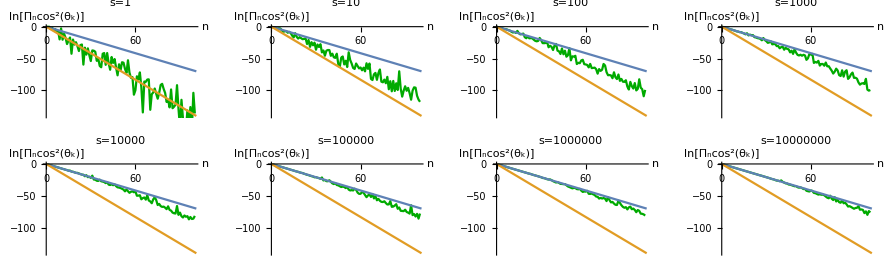
```mathematica
Export["LogCosMean.svg",-Graphics-];
```

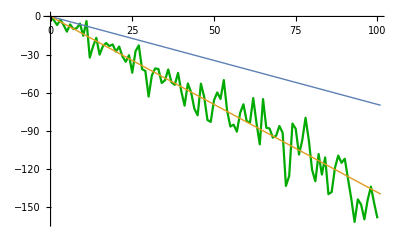

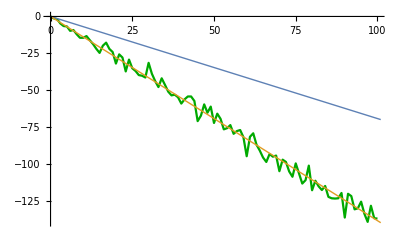

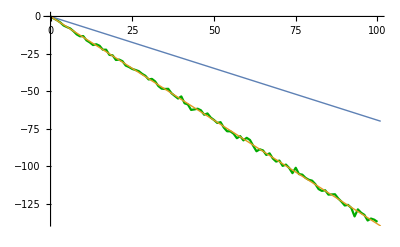

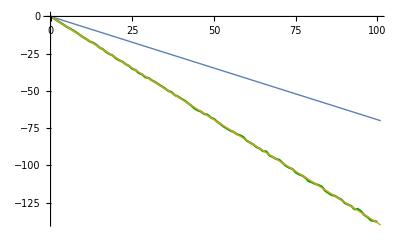

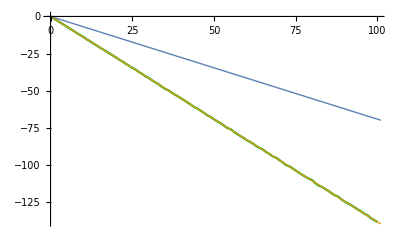

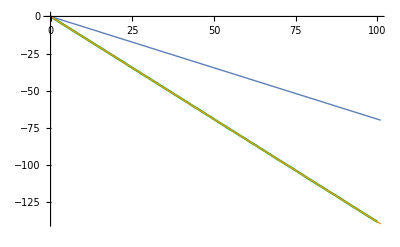

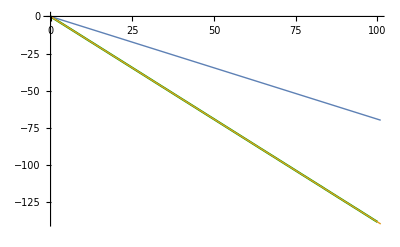

```mathematica
"MEAN OF LOGS";
ProductCosLogListPlot[{0,-2.9296,-6.72453,-2.66139,-6.74039,-11.9663,-6.27071,-9.94264,-9.25159,-5.60104,-15.2494,-3.62676,-32.4198,-23.6401,-16.8135,-30.0846,-23.4937,-20.9093,-23.3005,-22.054,-27.6412,-23.7147,-31.5786,-35.713,-30.5268,-44.3458,-27.3357,-22.8194,-41.4778,-43.0027,-63.1363,-46.3517,-40.959,-41.4105,-52.4005,-50.3991,-41.7816,-51.9325,-53.8725,-44.4549,-59.0093,-70.2833,-52.7955,-59.805,-72.8075,-77.9189,-52.9933,-63.4635,-81.6214,-83.0761,-66.0442,-59.8888,-65.0164,-50.1294,-74.1159,-86.7313,-85.2769,-90.7771,-75.9951,-69.2118,-82.5623,-83.6741,-64.334,-84.0453,-100.814,-65.1205,-87.6979,-88.2787,-95.5096,-93.9704,-86.3455,-91.6869,-133.551,-125.697,-84.3899,-88.5666,-108.819,-97.4419,-79.8382,-97.4457,-120.835,-129.861,-108.43,-124.572,-111.136,-140.004,-138.362,-119.211,-109.687,-115.304,-112.145,-128.084,-143.841,-161.905,-144.141,-148.332,-159.885,-144.654,-134.087,-147.269,-159.089}]
ProductCosLogListPlot[{0,-1.30277,-1.81781,-4.77234,-6.52858,-6.74368,-9.77713,-9.21558,-12.0746,-14.462,-14.4801,-13.3144,-16.078,-18.7416,-21.9571,-24.7435,-19.8581,-17.7829,-22.0321,-24.1564,-31.9858,-25.7447,-27.8762,-37.3338,-29.2824,-35.168,-37.0285,-39.8061,-40.2443,-41.4406,-31.4844,-38.8962,-43.8522,-47.9295,-41.9856,-46.4321,-51.0457,-53.5706,-53.1149,-54.8729,-59.1372,-56.2746,-54.3255,-54.3355,-57.4026,-71.0589,-67.3493,-59.6892,-65.3546,-61.1906,-72.3192,-66.0034,-69.4934,-76.6484,-75.8449,-73.7489,-79.666,-77.8065,-77.1036,-81.9757,-94.8944,-81.7064,-79.3215,-87.0555,-91.043,-95.76,-98.7854,-93.3936,-95.2053,-94.4383,-105.054,-97.2306,-98.7583,-105.237,-108.834,-99.7437,-106.547,-113.444,-111.143,-101.278,-117.999,-111.53,-115.308,-117.848,-115.077,-122.492,-123.445,-123.627,-123.451,-119.837,-136.532,-120.389,-121.962,-130.952,-130.24,-125.74,-133.926,-139.473,-128.512,-136.959,-137.24}]
ProductCosLogListPlot[{0,-1.32897,-2.55365,-4.02266,-6.05786,-7.09202,-7.98761,-9.80616,-11.9779,-13.2506,-13.1204,-15.9738,-17.3265,-19.0897,-18.5601,-19.5765,-22.2248,-22.1946,-25.6567,-25.9727,-29.0673,-28.8247,-29.887,-32.8182,-33.7828,-35.0787,-35.7658,-36.5529,-38.3297,-39.6263,-42.0794,-41.7053,-43.401,-46.5159,-48.2337,-48.4424,-48.3378,-51.3075,-53.1042,-54.8244,-53.4076,-57.9991,-58.7829,-62.4289,-62.0996,-61.6258,-62.6959,-65.6649,-64.7988,-67.557,-69.1683,-71.1435,-70.6111,-74.2199,-76.6981,-76.7333,-78.3382,-81.3292,-79.9576,-82.793,-81.0774,-82.5235,-86.4184,-90.0638,-88.7488,-89.4975,-92.513,-91.4564,-94.9269,-96.9346,-96.2871,-99.8283,-98.9612,-101.236,-104.675,-101.093,-105.308,-105.672,-107.836,-109.11,-109.697,-112.022,-115.334,-116.526,-116.099,-119.023,-118.905,-118.783,-121.572,-123.729,-126.277,-125.885,-127.926,-133.584,-128.875,-131.127,-132.552,-136.32,-134.997,-135.75,-137.246}]
ProductCosLogListPlot[{0,-1.31508,-2.79821,-4.08574,-5.52159,-7.03535,-8.17694,-9.47236,-10.876,-12.426,-13.9671,-15.2334,-16.8033,-17.6429,-19.0733,-20.9075,-21.9932,-23.8638,-25.1875,-26.216,-28.128,-29.402,-30.3637,-32.0186,-33.2073,-35.1411,-35.9734,-38.0266,-38.8558,-40.8045,-41.3218,-42.9038,-44.0909,-45.4812,-46.8725,-48.3095,-49.9675,-50.7929,-52.8033,-53.781,-55.2289,-56.4582,-58.1538,-59.7411,-61.7168,-63.0254,-63.849,-65.4864,-65.9292,-67.8783,-68.8259,-70.7135,-72.2852,-73.9433,-75.3696,-76.6409,-77.5806,-79.0536,-79.8056,-81.0579,-83.4024,-84.6639,-85.9247,-87.7235,-88.7433,-90.4378,-90.6233,-93.4142,-94.3635,-95.6846,-96.3281,-98.37,-100.307,-101.584,-102.433,-104.733,-106.012,-106.831,-108.373,-110.632,-111.39,-112.441,-113.278,-114.223,-117.019,-118.507,-119.905,-120.465,-121.87,-122.989,-125.247,-126.308,-127.302,-129.493,-129.246,-130.875,-133.37,-134.744,-136.926,-137.343,-137.937}]
ProductCosLogListPlot[{0,-1.40037,-2.79226,-4.16144,-5.50092,-6.92594,-8.35786,-9.6577,-11.1461,-12.4739,-13.7523,-15.3072,-16.6381,-18.073,-19.3987,-20.868,-22.1515,-23.5095,-24.9558,-26.2419,-27.6502,-29.1376,-30.3781,-31.9547,-33.2329,-34.7438,-35.8073,-37.4627,-38.7743,-40.3099,-41.5008,-43.03,-44.3783,-45.7002,-47.2966,-48.7771,-49.7816,-51.2733,-52.7158,-53.972,-55.3665,-56.7648,-58.1908,-59.667,-61.1513,-62.3123,-63.6954,-65.1368,-66.7429,-67.8533,-69.3876,-70.7683,-72.0133,-73.5504,-75.1419,-76.013,-77.6807,-79.2139,-80.582,-81.8702,-83.3717,-84.6571,-85.9105,-87.5768,-88.8056,-89.8928,-91.5956,-92.818,-94.456,-95.3456,-96.9304,-98.4443,-100.186,-101.087,-102.475,-103.967,-105.424,-106.849,-108.257,-109.426,-110.529,-112.456,-113.997,-115.034,-116.393,-117.732,-119.312,-120.71,-121.677,-123.467,-124.983,-126.185,-127.425,-128.804,-130.299,-131.598,-133.091,-134.264,-136.075,-137.375,-138.629}]
ProductCosLogListPlot[{0,-1.38511,-2.7743,-4.1609,-5.53747,-6.95397,-8.32794,-9.69641,-11.0762,-12.4762,-13.8983,-15.2099,-16.641,-18.0319,-19.4077,-20.7852,-22.1463,-23.5381,-24.9401,-26.3386,-27.7108,-29.1074,-30.4348,-31.8469,-33.3177,-34.651,-36.0603,-37.4071,-38.8166,-40.2249,-41.5131,-42.973,-44.3775,-45.7816,-47.0947,-48.5191,-49.8506,-51.2805,-52.6963,-54.054,-55.4237,-56.82,-58.2008,-59.6601,-61.0426,-62.3136,-63.7455,-65.1311,-66.572,-67.8783,-69.3345,-70.7272,-72.1071,-73.5061,-74.9324,-76.2698,-77.5835,-79.038,-80.4361,-81.7382,-83.1451,-84.5948,-85.9539,-87.2338,-88.7828,-90.0349,-91.5022,-92.8934,-94.2785,-95.7337,-97.0781,-98.3749,-99.8217,-101.194,-102.49,-103.939,-105.302,-106.703,-108.183,-109.586,-110.931,-112.356,-113.704,-115.036,-116.397,-117.881,-119.212,-120.531,-121.945,-123.328,-124.754,-126.157,-127.616,-128.928,-130.311,-131.705,-133.145,-134.518,-135.847,-137.262,-138.62}]
ProductCosLogListPlot[{0,-1.38828,-2.7714,-4.15793,-5.54035,-6.93469,-8.3143,-9.69968,-11.0788,-12.4795,-13.8604,-15.2581,-16.6519,-18.008,-19.3994,-20.7936,-22.1754,-23.5539,-24.9561,-26.3381,-27.7217,-29.0972,-30.49,-31.8769,-33.2563,-34.656,-36.0391,-37.4224,-38.8081,-40.1914,-41.5888,-42.9608,-44.3739,-45.7401,-47.1488,-48.5048,-49.9031,-51.2951,-52.6884,-54.0712,-55.4662,-56.8422,-58.2156,-59.613,-60.9897,-62.3789,-63.7778,-65.1585,-66.5502,-67.936,-69.292,-70.7022,-72.0884,-73.4703,-74.8645,-76.2407,-77.6387,-79.017,-80.4078,-81.8046,-83.1764,-84.5669,-85.9624,-87.3537,-88.752,-90.1102,-91.5069,-92.8918,-94.2619,-95.6367,-97.054,-98.422,-99.8238,-101.184,-102.577,-103.965,-105.358,-106.755,-108.117,-109.51,-110.902,-112.276,-113.663,-115.016,-116.465,-117.825,-119.235,-120.617,-122.021,-123.374,-124.787,-126.139,-127.537,-128.93,-130.28,-131.691,-133.09,-134.473,-135.863,-137.273,-138.604}]
```

```mathematica
Show[DiscretePlot[list[[k+1]],{k,0,Length[list]-1},PlotRange->{-Log[4]Length[list],0},PlotStyle->Darker[Green],Filling->None,Joined->True,PlotLabel->"s="<>ToString[s],AxesLabel->{n,"Π_ncos^2(θ_k)"}],Plot[{-Log[2],-Log[4]},{x,0,600},PlotStyle->{}]]
```

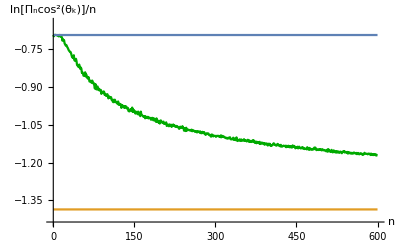

```mathematica
With[{list={-0.693147,-0.698276,-0.69272,-0.693104,-0.692734,-0.693175,-0.693706,-0.693449,-0.695385,-0.695347,-0.698596,-0.697065,-0.692806,-0.69858,-0.69708,-0.700389,-0.701852,-0.715804,-0.710278,-0.714099,-0.713837,-0.726808,-0.730519,-0.735009,-0.732556,-0.736425,-0.741819,-0.745139,-0.75062,-0.755094,-0.757363,-0.760391,-0.760692,-0.766541,-0.774702,-0.781871,-0.781273,-0.784882,-0.77364,-0.792691,-0.795575,-0.791485,-0.787687,-0.797058,-0.812527,-0.814617,-0.818175,-0.820293,-0.810597,-0.822694,-0.827642,-0.822356,-0.827569,-0.84375,-0.841104,-0.845981,-0.855254,-0.854215,-0.854261,-0.841311,-0.857876,-0.849897,-0.858487,-0.863379,-0.866348,-0.859943,-0.866699,-0.877836,-0.8784,-0.875179,-0.877615,-0.883449,-0.874041,-0.879628,-0.885568,-0.884582,-0.894595,-0.906,-0.888034,-0.897172,-0.909382,-0.898092,-0.897714,-0.91026,-0.912173,-0.906763,-0.913822,-0.912575,-0.911449,-0.927132,-0.920385,-0.918822,-0.922348,-0.917224,-0.918574,-0.930925,-0.926823,-0.932094,-0.935589,-0.930127,-0.928333,-0.932804,-0.945043,-0.936893,-0.938483,-0.941094,-0.943533,-0.940148,-0.951258,-0.950358,-0.957363,-0.960147,-0.950311,-0.959765,-0.950361,-0.956139,-0.960268,-0.960774,-0.965121,-0.962344,-0.957103,-0.970532,-0.966605,-0.966599,-0.971009,-0.968567,-0.982686,-0.971474,-0.975255,-0.973988,-0.979616,-0.981745,-0.975239,-0.98245,-0.976513,-0.977386,-0.982303,-0.986402,-0.982666,-0.994731,-0.99603,-0.99674,-0.989305,-0.991967,-0.987715,-0.993471,-0.981564,-0.99887,-0.989295,-0.998261,-0.993684,-0.99846,-1.00535,-0.997787,-1.00258,-1.00269,-1.00783,-0.997572,-1.00836,-1.00247,-1.01006,-1.01555,-0.997647,-1.00903,-1.01077,-1.01319,-1.0159,-1.01821,-1.01888,-1.01532,-1.02421,-1.01707,-1.01933,-1.0223,-1.02015,-1.01832,-1.02444,-1.02283,-1.02117,-1.02328,-1.0259,-1.02994,-1.0243,-1.02219,-1.02723,-1.03191,-1.02392,-1.03238,-1.03132,-1.02991,-1.03797,-1.02443,-1.03818,-1.03299,-1.03367,-1.04174,-1.03894,-1.04505,-1.03344,-1.03238,-1.03854,-1.03755,-1.04277,-1.04099,-1.03726,-1.04628,-1.04346,-1.04624,-1.04316,-1.04026,-1.05463,-1.05089,-1.04956,-1.05041,-1.05589,-1.04842,-1.05142,-1.0528,-1.04957,-1.05834,-1.05315,-1.05153,-1.04863,-1.05453,-1.05136,-1.05488,-1.05817,-1.05564,-1.05435,-1.05885,-1.05697,-1.05937,-1.06257,-1.06607,-1.06045,-1.05749,-1.06087,-1.06206,-1.06209,-1.0554,-1.06207,-1.0626,-1.07341,-1.06454,-1.06365,-1.07477,-1.06163,-1.07307,-1.07176,-1.06986,-1.06922,-1.0714,-1.07123,-1.07053,-1.07337,-1.07121,-1.06925,-1.07545,-1.07475,-1.07157,-1.07404,-1.07439,-1.07762,-1.07525,-1.07574,-1.07552,-1.08037,-1.07651,-1.07553,-1.07666,-1.07773,-1.08124,-1.07619,-1.08242,-1.08354,-1.0818,-1.0779,-1.08292,-1.08342,-1.07872,-1.0827,-1.08704,-1.09007,-1.0859,-1.08344,-1.08608,-1.08656,-1.08431,-1.0899,-1.09123,-1.09008,-1.09297,-1.09716,-1.08852,-1.08914,-1.09022,-1.09596,-1.09443,-1.09353,-1.09373,-1.09409,-1.09774,-1.09533,-1.09348,-1.09478,-1.09434,-1.09386,-1.09729,-1.09647,-1.09889,-1.09191,-1.09969,-1.09347,-1.09805,-1.09544,-1.09557,-1.09784,-1.10058,-1.09995,-1.10146,-1.10365,-1.10158,-1.10375,-1.10525,-1.10111,-1.10231,-1.1028,-1.0994,-1.10651,-1.10801,-1.10611,-1.10692,-1.10724,-1.10113,-1.1096,-1.10489,-1.1091,-1.10903,-1.11116,-1.09997,-1.1117,-1.11444,-1.11221,-1.11204,-1.10873,-1.10789,-1.11411,-1.11229,-1.10825,-1.11296,-1.11276,-1.11021,-1.11162,-1.10723,-1.11393,-1.11091,-1.11174,-1.11352,-1.11604,-1.11292,-1.10944,-1.11279,-1.11742,-1.11202,-1.11715,-1.11564,-1.11733,-1.11827,-1.11514,-1.11128,-1.11653,-1.11206,-1.11604,-1.12173,-1.11781,-1.11672,-1.12324,-1.11772,-1.12013,-1.11866,-1.12124,-1.12389,-1.11757,-1.12625,-1.12547,-1.1236,-1.1203,-1.12382,-1.12551,-1.12218,-1.1229,-1.12923,-1.12381,-1.12581,-1.1277,-1.12406,-1.12725,-1.13232,-1.12597,-1.12505,-1.12961,-1.12574,-1.13318,-1.13127,-1.13309,-1.13153,-1.12971,-1.12548,-1.12337,-1.12751,-1.12953,-1.1292,-1.13247,-1.1327,-1.12905,-1.12586,-1.13116,-1.12913,-1.13278,-1.13107,-1.13568,-1.12957,-1.13607,-1.13391,-1.13627,-1.13416,-1.13279,-1.13431,-1.13387,-1.13539,-1.13312,-1.13901,-1.13363,-1.13771,-1.1375,-1.13319,-1.13421,-1.13924,-1.13525,-1.13441,-1.13982,-1.13994,-1.14,-1.13172,-1.13773,-1.13798,-1.13404,-1.13867,-1.1434,-1.14087,-1.13856,-1.14183,-1.1371,-1.14361,-1.14192,-1.1369,-1.14071,-1.14173,-1.14398,-1.14237,-1.13954,-1.14335,-1.13982,-1.14427,-1.14359,-1.14635,-1.14511,-1.1445,-1.14465,-1.14757,-1.13893,-1.14579,-1.14744,-1.14907,-1.14181,-1.14793,-1.14504,-1.14674,-1.14939,-1.1477,-1.14577,-1.14806,-1.14468,-1.14062,-1.14684,-1.14043,-1.14563,-1.15065,-1.14954,-1.14714,-1.14993,-1.15002,-1.14757,-1.14644,-1.15014,-1.14759,-1.14965,-1.15184,-1.1469,-1.14966,-1.15013,-1.15191,-1.15012,-1.15117,-1.15211,-1.15549,-1.15382,-1.14885,-1.1571,-1.14655,-1.15195,-1.15427,-1.15393,-1.15788,-1.15241,-1.14959,-1.15626,-1.15932,-1.15856,-1.15152,-1.1569,-1.15533,-1.15997,-1.15694,-1.15448,-1.16072,-1.15713,-1.15583,-1.15711,-1.16164,-1.15839,-1.15628,-1.15906,-1.15977,-1.16293,-1.15649,-1.15746,-1.15799,-1.1542,-1.15987,-1.15686,-1.15857,-1.16017,-1.15929,-1.15781,-1.16417,-1.15943,-1.1629,-1.1598,-1.16193,-1.16412,-1.16082,-1.16307,-1.16488,-1.16325,-1.16071,-1.16358,-1.16039,-1.16192,-1.1632,-1.16465,-1.16177,-1.16663,-1.16417,-1.1619,-1.16281,-1.16749,-1.16615,-1.16529,-1.16265,-1.16445,-1.1655,-1.16896,-1.16551,-1.16822,-1.16525,-1.16124,-1.16415,-1.16525,-1.16531,-1.16474,-1.16575,-1.16742,-1.16466,-1.16436,-1.16511,-1.16651,-1.17007,-1.16429,-1.16838,-1.16795,-1.16727,-1.17037,-1.16613,-1.16889,-1.16792,-1.17054,-1.16753,-1.17218,-1.17005,-1.17001}},Show[DiscretePlot[list[[k+1]],{k,0,Length[list]-1},PlotRange->{-Log[4]-1/20,-Log[2]+1/20},PlotStyle->Darker[Green],Filling->None,Joined->True,AxesLabel->{n,"ln[Π_ncos^2(θ_k)]/n"}],Plot[{-Log[2],-Log[4]},{x,0,600},PlotStyle->{}]]]
```

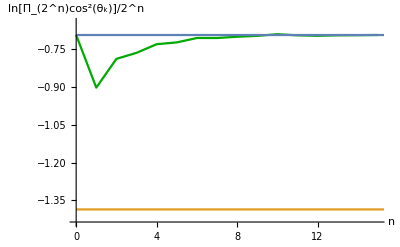

```mathematica
With[{list={-0.693147,-0.902231,-0.787913,-0.763978,-0.729643,-0.7225,-0.705001,-0.70502,-0.699968,-0.696476,-0.68995,-0.694445,-0.69622,-0.694352,-0.693828,-0.693059}},Show[DiscretePlot[list[[k+1]],{k,0,Length[list]-1},PlotRange->{-Log[4]-1/20,-Log[2]+1/20},PlotStyle->Darker[Green],Filling->None,Joined->True,AxesLabel->{n,"ln[Π_(2^n)cos^2(θ_k)]/2^n"}],Plot[{-Log[2],-Log[4]},{x,0,600},PlotStyle->{}]]]
```